```mathematica
Clear["@"];
```

Clear::wrsym: Symbol a is Protected.

Clear::wrsym: Symbol b is Protected.

Clear::wrsym: Symbol c is Protected.

General::stop: Further output of Clear :: wrsym will be suppressed during this calculation.

```mathematica
(*Remove["W`KNN`*"]*)
```

```mathematica
<<ICA`;
<<PCA`;
<<matcher`;
<<classifier`;
<<Data`;
```

Needs::nocont: Context "KNN`" was not created when Needs was evaluated.

```mathematica
(*Names["W`KNN`*"]*)
```

{Distancef,KNN}

```mathematica
data=nxrData[-1];
Dimensions[data]
```

{50,2,6,46}

```mathematica
pd=Flatten[data,{{1},{2},{3,4}}];
```

# Use Arch I, that is, use each measure as signal, each feature(like freq) as sample

## use one person’s two measures

### original data

```mathematica
pd1=pd[[1]];
Dimensions[%]
```

{2,276}

```mathematica
{ic,W,A}=fastICA[pd1,retW->True(*,noMean->False*)];
(* to use other data,must be centered*)
```

use deltaW:1/1000, Maxstep:100

Smallest remaining (non-zero) eigenvalue 0.0381187

Largest remaining (non-zero) eigenvalue 1.65412

whiten OK

guess OK

total time:0.09375seconds

```mathematica
Dimensions[ic]
```

{2,276}

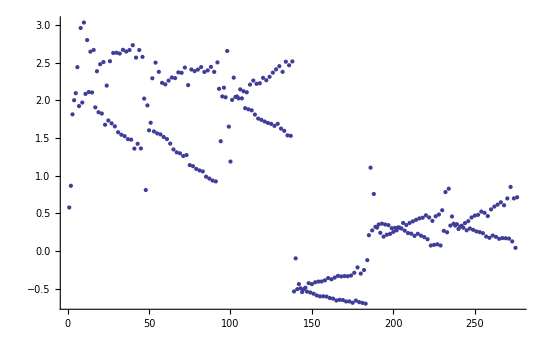

```mathematica
ListPlot[pd1[[1]]]
```

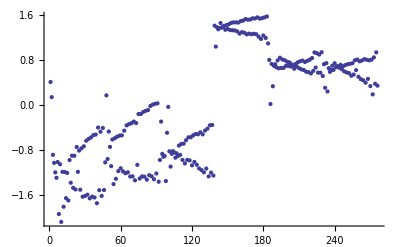

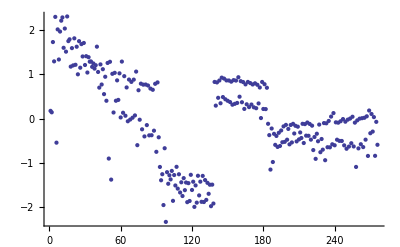

```mathematica
ListPlot[ic[[1]]]
ListPlot[ic[[2]]]
```

```mathematica
nic=ic/√Length[ic[[1]]];
nic.nicᵀ
```

{{0.996377,2.92157×10^-16},{2.92157×10^-16,0.996377}}

```mathematica
Max[Chop[A.ic-Standardize[pd1ᵀ,Mean,1&]ᵀ]]
```

0

```mathematica
ic.icᵀ
```

{{275.,-3.0444×10^-14},{-3.0444×10^-14,275.}}

{{0.996377,-1.14303×10^-16},{-1.14303×10^-16,0.996377}}

```mathematica
Standardize[pd1ᵀ,Mean,1&]ᵀ.nicᵀ
```

{{-17.5194,-1.42501},{-11.4505,-4.85863}}

```mathematica
pd2=pd[[2]];
cpd2=Standardize[pd2ᵀ,Mean,1&]ᵀ;
cpd2.icᵀ
```

{{-14.1598,14.2881},{12.3144,5.09495}}

```mathematica
cpd3=Standardize[pd[[3]]ᵀ,Mean,1&]ᵀ;
cpd3.nicᵀ
```

{{0.23055,-0.451041},{-0.378367,0.629805}}

```mathematica
(* project data into new basis*)
cd=Table[rowMean[pd[[i]]].nicᵀ,{i,2,Length[pd]}];
Dimensions[%]
ncd=Table[Map[Normalize[#]&,rowMean[pd[[i]]].icᵀ],{i,2,Length[pd]}];
Dimensions[%]
```

{49,2,2}

{49,2,2}

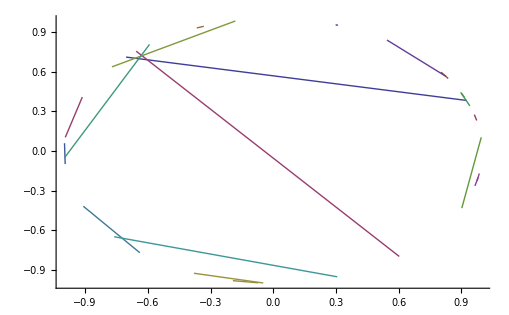

```mathematica
Show[ListPlot[ncd[[;;20]],Joined->True](*ListPlot[cd[[;;20]],Joined->True]*)]
```

```mathematica
sj1=Table[J1[ncd[[;;,;;,i]]],{i,Length[cd[[1,1]]]}]
ListPlot[sj1,Joined->True,PlotRange->{5,6},Mesh->Full]
(* good*)
```

{6.18247,3.12364}

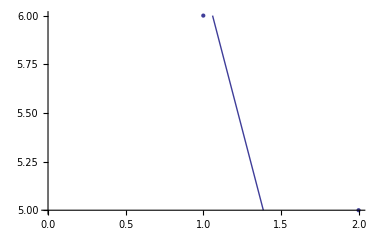

```mathematica
sj1=Table[J1[cd[[;;,;;,i]]],{i,Length[cd[[1,1]]]}]
ListPlot[sj1,Joined->True,PlotRange->{5,6},Mesh->Full]
```

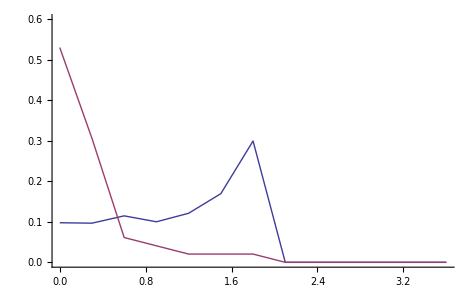

```mathematica
{dd,ds}=eucDist[ncd[[;;,;;]]];
dt=DistList[{dd,ds},{0,4,0.3}];
ListPlot[dt,Joined->True,PlotRange->{0,0.6}]
(* looks very good ..*)
```

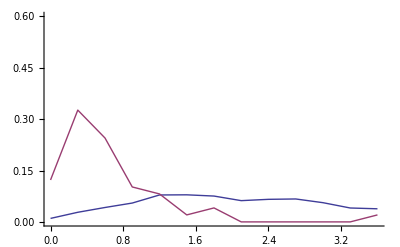

```mathematica
{dd,ds}=eucDist[cd[[;;,;;]]];
dt=DistList[{dd,ds},{0,4,0.3}];
ListPlot[dt,Joined->True,PlotRange->{0,0.6}]
```

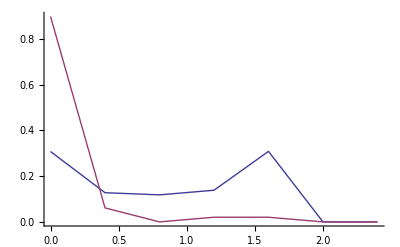

```mathematica
(* try cosdist dist*)
(* when using cosdist, data is actually first normalized.so normalization before does never matter*)
{dd,ds}=dDist[ncd(*[[;;,;;,2]]*),CosineDistance];

dt=DistList[{dd,ds},{0,3,0.4}];
ListPlot[dt,Joined->True]
```

```mathematica
TTest[{dd,ds},0,{"TestDataTable","TestConclusion"},SignificanceLevel->.0001]
```

TTest::nortst: At least one of the p-values in {0., 0.}, resulting from a test for normality, is below 0.00005. The tests in {"T"} require that the data is normally distributed.

Intersection::normal: Nonatomic expression expected at position 2 in {"PairedT", "T", "Z", "KSampleT"} ∩ "T".

TTest::nortst: At least one of the p-values in {0., 0.}, resulting from a test for normality, is below 0.00005. The tests in {"PairedT", "T", "Z", "KSampleT"} ∩ "T" require that the data is normally distributed.

General::stop: Further output of TTest :: nortst will be suppressed during this calculation.

{ | Statistic | P-Value
T | 16.27 | 4.61987×10^-22,The null hypothesis that the median difference is 0 is rejected at the 0.01 percent level based on the T test.}

```mathematica
is=cd;
templ=is[[All,1]];
pdata=is[[All,2]];
tg=ConstantArray[ConstantArray[0,Length[templ]],Length[pdata]];
For[i=1;k=1;n=1,i≤Length[pdata],i++,
For[m=1,m≤1,m++,
tg[[n,k]]=1;
n++;
];
k++;
];
```

```mathematica
tg;
```

```mathematica
(*euclidean classify*)
EER[pdata,templ,tg,classifyDist1,{0,2,0.005}]
(*cos c*)
EER[pdata,templ,tg,classifyDist2,{0,2,0.005}]
```

{1.325,{0.16369,0.163265}}

{0.165,{0.178997,0.183673}}

```mathematica
(* use first ic,eer=0.2,second 0.28,two together 0.175
using cos dist eer= 0.18*)
(* when using non-normal data, euclidean eer=16.3%*)
```

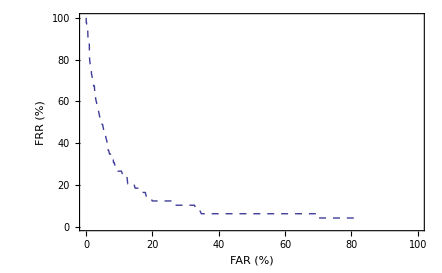

```mathematica
r1=RocPlot[pdata,templ,tg,classifyDist1,{0,6,0.02},1]
```

```mathematica
(*let us try KNN*)
(* number of k does not matter here*)
pg=KNN[pdata,templ,tg,K->10];
```

Warning: k is bigger than num of samples in a class

```mathematica
Diagonal[ pg];
Dimensions[pg];
VF[tg,pg]
```

{0,0,1,0,0,1,1,0,0,1,1,0,0,0,1,1,0,0,1,1,1,0,0,0,1,1,1,1,0,0,1,1,0,0,0,0,0,0,1,0,0,0,0,1,0,0,1,0,0}

{49,49}

{0.0249896,0.0127551,0.612245}

### maybe the average of one person’s data can make it better?? the mean erases the diff of classes (No way...)

```mathematica
mpd=Total[pd]/Length[pd];
Dimensions[mpd]
```

{2,276}

```mathematica
{ic,W,A}=fastICA[mpd,retW->True(*,noMean->False*)];
```

use deltaW:1/1000, Maxstep:100

Dimension adjusted to 1 according to covariance matrix

Sum of 1 removed eigenvalues(Choped) 0

100.% of (non-zero) eigenvalues retained

Smallest remaining (non-zero) eigenvalue 0.00183905

Largest remaining (non-zero) eigenvalue 0.00183905

whiten OK

guess OK

total time:0.046875seconds

```mathematica
nic=ic/√Length[ic[[1]]];
nic.nicᵀ
cd=Table[rowMean[pd[[i]]].nicᵀ,{i,2,Length[pd]}];
Dimensions[%]
ncd=Table[Map[Normalize[#]&,rowMean[pd[[i]]].icᵀ],{i,2,Length[pd]}];
Dimensions[%]
```

{{0.996377}}

{49,2,1}

{49,2,1}

```mathematica
Dimensions[ic]
```

{1,276}

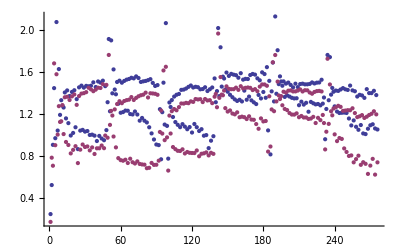

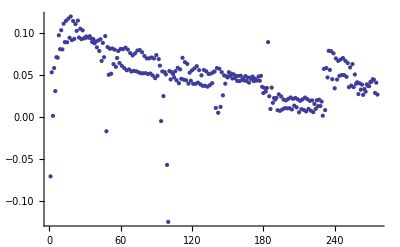

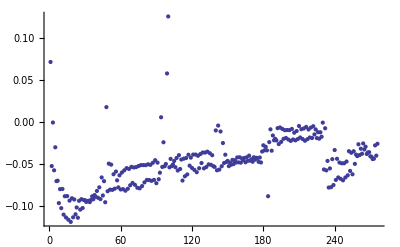

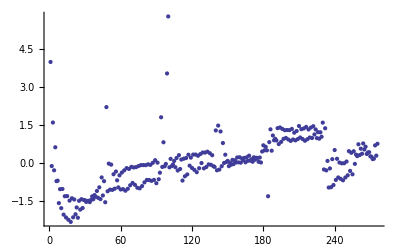

```mathematica
ListPlot[pd[[5]]]
ListPlot[mpd[[1]]]
ListPlot[mpd[[2]]]
ListPlot[ic[[1]]]
```

{1.5143}

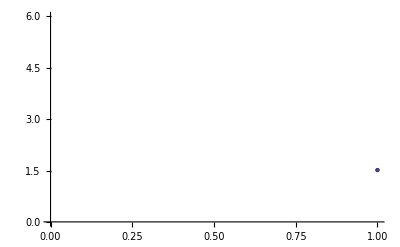

```mathematica
sj1=Table[J1[cd[[;;,;;,i]]],{i,Length[cd[[1,1]]]}]
ListPlot[sj1,Joined->True,PlotRange->{0,6},Mesh->Full]
```

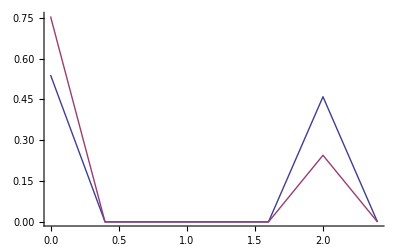

```mathematica
{dd,ds}=dDist[ncd(*[[;;,;;,2]]*),CosineDistance];
dt=DistList[{dd,ds},{0,3,0.4}];
ListPlot[dt,Joined->True]
(*it should not be normalized*)
```

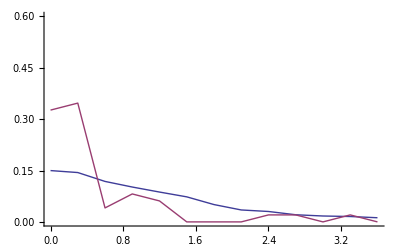

```mathematica
{dd,ds}=eucDist[cd[[;;,;;]]];
dt=DistList[{dd,ds},{0,4,0.3}];
ListPlot[dt,Joined->True,PlotRange->{0,0.6}]
```

```mathematica
is=cd;
templ=is[[All,1]];
pdata=is[[All,2]];
tg=ConstantArray[ConstantArray[0,Length[templ]],Length[pdata]];
For[i=1;k=1;n=1,i≤Length[pdata],i++,
For[m=1,m≤1,m++,
tg[[n,k]]=1;
n++;
];
k++;
];
```

```mathematica
EER[pdata,templ,tg,classifyDist1,{0,2,0.005}]
```

{0.685,{0.326531,0.326531}}

```mathematica
pg=KNN[pdata,templ,tg,K->1];
VF[tg,pg]
```

{0.0366514,0.0187075,0.897959}

## use one measure of all persons

```mathematica
mp=pd[[All,1]];
Dimensions[%]
```

{50,276}

```mathematica
{ic,W,A}=fastICA[mp,retW->True];
```

use deltaW:1/1000, Maxstep:100

Smallest remaining (non-zero) eigenvalue 0.00012965

Largest remaining (non-zero) eigenvalue 6.17297

whiten OK

guess OK

1 Failed to converge, try again

2 Failed to converge, try again

3 Failed to converge, try again

1 Failed to converge, try again

1 Failed to converge, try again

2 Failed to converge, try again

3 Failed to converge, try again

4 Failed to converge, try again

5 Failed to converge, try again

49 6 Failed to converge, give up

total time:1.25seconds

failed 1 times, try from the beginning

guess OK

1 Failed to converge, try again

1 Failed to converge, try again

1 Failed to converge, try again

«1 more identical outputs»

total time:1.375seconds

```mathematica
Dimensions[ic]
```

{50,276}

```mathematica
nic=ic/√Length[ic[[1]]];
```

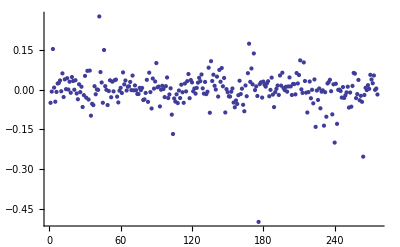

```mathematica
ListPlot[nic[[20]]]
```

```mathematica
Chop[nic.nicᵀ];
```

```mathematica
Total[pd[[3,1]]]
```

-61.138

```mathematica
W.rowMean[mp]==ic
Max[Chop[W.A]]
```

True

```mathematica
Max[Chop[A.ic-rowMean[mp]]]
```

```mathematica
mp[[3]]==pd[[3]][[1]]
```

True

```mathematica
(* since ic.icᵀ=275 I, rowMean[mp].icᵀ== 275 A*)
```

```mathematica
rowMean[mp].icᵀ/A;
```

```mathematica
pd[[3]][[1]].icᵀ
```

{275.,275.,275.,275.,275.,275.,275.,275.,275.,275.,275.,275.,275.,275.,275.,275.,275.,275.,275.,275.,275.,275.,275.,275.,275.,275.,275.,275.,275.,275.,275.,275.,275.,275.,275.,275.,275.,275.,275.,275.,275.,275.,275.,275.,275.,275.,275.,275.,275.,275.}

```mathematica
cd=Table[rowMean[pd[[i]]].nicᵀ,{i,1,Length[pd]}];
Dimensions[%]
ncd=Table[Map[Normalize[#]&,rowMean[pd[[i]]].icᵀ],{i,1,Length[pd]}];
Dimensions[%]
```

{50,2,50}

{50,2,50}

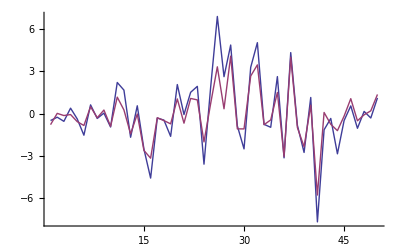

```mathematica
ListPlot[cd[[1]],Joined->True]
(*Much much better*)
```

{0.808879,2.8098,3.9576,2.45666,3.05705,1.55768,1.69949,1.12605,0.96103,2.32336,4.72468,1.11499,5.3195,4.31329,2.14362,6.0479,1.69632,1.3848,2.64705,2.56491,9.73821,9.04694,3.24241,8.5629,1.02084,5.67901,1.53269,11.474,8.85198,2.33784,3.43476,10.9051,1.5932,6.76995,3.12875,4.99535,8.80988,6.57262,3.26929,1.66979,4.39539,2.24767,2.15959,1.77076,1.63193,7.25525,4.62032,7.43555,4.64101,10.4685}

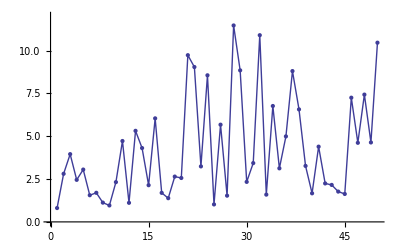

```mathematica
sj1=Table[J1[cd[[;;,;;,i]]],{i,Length[cd[[1,1]]]}]
ListPlot[sj1,Joined->True,PlotRange->{0,12},Mesh->Full]
```

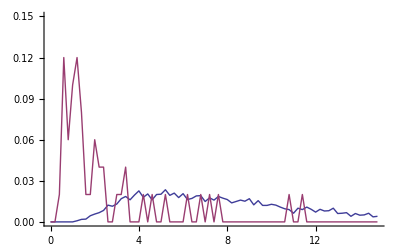

```mathematica
(*check all feature data first*)
{dd,ds}=eucDist[cd[[;;,;;]]];
dt=DistList[{dd,ds},{0,15,0.2}];
ListPlot[dt,Joined->True,PlotRange->{0,0.15}]
```

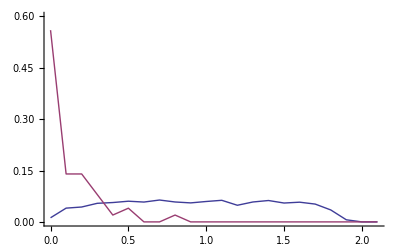

```mathematica
{dd,ds}=dDist[cd(*[[;;,;;,2]]*),CosineDistance];
dt=DistList[{dd,ds},{0,2.2,0.1}];
ListPlot[dt,Joined->True,PlotRange->{0,0.6}]
(*Cosine is really better here*)
```

```mathematica
is=cd;
templ=is[[All,1]];
pdata=is[[All,2]];
tg=ConstantArray[ConstantArray[0,Length[templ]],Length[pdata]];
For[i=1;k=1;n=1,i≤Length[pdata],i++,
For[m=1,m≤1,m++,
tg[[n,k]]=1;
n++;
];
k++;
];
```

```mathematica
EER[pdata,templ,tg,classifyDist1,{0,6,0.005}]
```

{4.645,{0.2,0.2}}

```mathematica
EER[pdata,templ,tg,classifyDist2,{0,2,0.001}]
```

{0.338,{0.111837,0.12}}

### Use J1 to select features.

```mathematica
oj1=Reverse[Ordering[sj1]]
```

{28,32,50,21,22,29,37,24,48,46,34,38,16,26,13,36,11,49,47,41,14,3,31,39,23,35,5,2,19,20,4,30,10,42,43,15,44,7,17,40,45,33,6,27,18,8,12,25,9,1}

```mathematica
geteer[s_,tg_,fc_]:=Module[
{pdata,templ},
pdata=s[[All,1]];
templ=s[[All,2]];
EER[pdata,templ,tg,fc,{0,6,0.005}]
];
```

```mathematica
(*e=Reap[For[i=1,i≤Length[cd[[1,1]]],i++,
Sow[Mean[geteer[cd[[;;,;;,;;i]],tg,classifyDist1][[2]]]];
Print[i];]][[2,1]];*)
```

1

2

3

4

5

6

7

8

9

10

11

12

13

14

15

16

17

18

19

20

21

22

23

24

25

26

27

28

29

30

31

32

33

34

35

36

37

38

39

40

41

42

43

44

45

46

47

48

49

50

```mathematica
(*Export["Cache_eICA1.mx",e]*)
e=Import["Cache_eICA1.mx"];
```

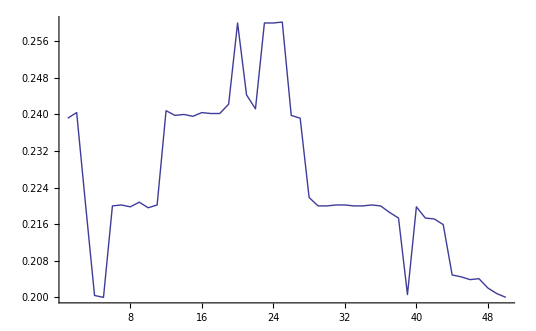

```mathematica
ListPlot[e,Joined->True]
```

```mathematica
(*e=Reap[For[i=1,i≤Length[oj1],i++,
Sow[Mean[geteer[cd[[;;,;;,oj1⟦;;i⟧]],tg,classifyDist1][[2]]]];
Print[i];]][[2,1]];*)
```

1

2

3

4

5

6

7

8

9

10

11

12

13

14

15

16

17

18

19

20

21

22

23

24

25

26

27

28

29

30

31

32

33

34

35

36

37

38

39

40

41

42

43

44

45

46

47

48

49

50

```mathematica
(*Export["Cache_eICA1_mda.mx",e]*)
e=Import["Cache_eICA1_mda.mx"];
```

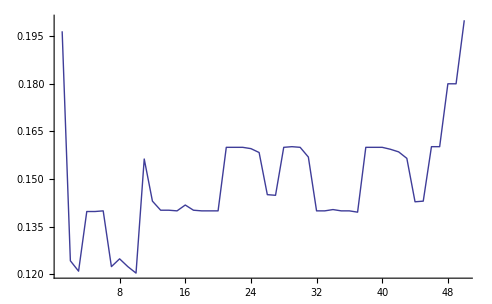

```mathematica
ListPlot[e,Joined->True]
(*order is important!!*)
```

### use average of two measures, this should be better since the random error is reduced..

```mathematica
apd=Map[Mean,pd];
Dimensions[apd]
```

{50,276}

```mathematica
{ic,W,A}=fastICA[apd,retW->True];
```

use deltaW:1/1000, Maxstep:100

Dimension adjusted to 49 according to covariance matrix

Sum of 1 removed eigenvalues(Choped) 0

100.% of (non-zero) eigenvalues retained

Smallest remaining (non-zero) eigenvalue 0.0000757775

Largest remaining (non-zero) eigenvalue 4.73416

whiten OK

guess OK

1 time(s) Failed to converge, try again

1 time(s) Failed to converge, try again

1 time(s) Failed to converge, try again

«1 more identical outputs»

total time:1.234375seconds

ICs computation successed!

```mathematica
(*a cached version of ics*)
(*Export["Cache_icICA1.mx",ic]*)
ic=Import["Cache_icICA1.mx"];
Dimensions[%]
```

{49,276}

```mathematica
MatrixRank[ic](*It is full rank*)
```

49

```mathematica
nic=ic/√Length[ic[[1]]];
cd=Table[rowMean[pd[[i]]].nicᵀ,{i,1,Length[pd]}];
Dimensions[%]
ncd=Table[Map[Normalize[#]&,rowMean[pd[[i]]].icᵀ],{i,1,Length[pd]}];
Dimensions[%]
```

{50,2,49}

{50,2,49}

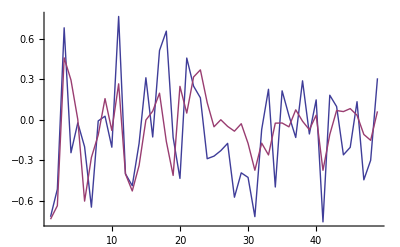

```mathematica
ListPlot[cd[[3]],Joined->True]
```

{4.14548,2.17568,3.23612,1.55921,0.959341,2.45624,2.19848,0.835463,0.933066,6.8221,1.53504,0.883438,1.57884,1.4476,5.44229,1.45789,4.8842,9.67775,1.45861,5.82768,7.16036,10.691,1.37848,2.02719,7.36315,1.00349,6.50034,14.37,1.6796,3.13802,1.57417,9.23765,4.63161,4.15213,1.92367,3.16534,7.35452,8.97435,4.29293,15.4528,3.04423,2.9409,10.4932,2.2828,1.66738,5.2887,3.06119,7.36455,2.68441}

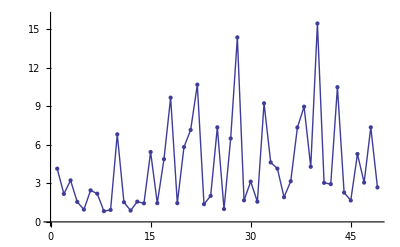

```mathematica
sj1=Table[J1[cd[[;;,;;,i]]],{i,Length[cd[[1,1]]]}]
ListPlot[sj1,Joined->True,PlotRange->{0,16},Mesh->Full]
```

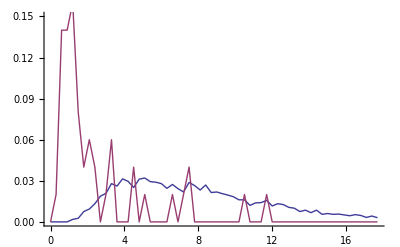

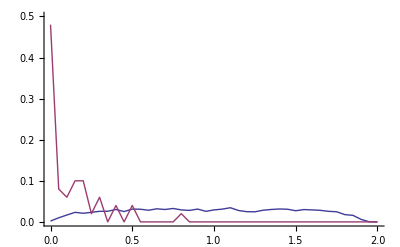

```mathematica
{dd,ds}=eucDist[cd[[;;,;;]]];
dt=DistList[{dd,ds},{0,18,0.3}];
ListPlot[dt,Joined->True,PlotRange->{0,0.15}]
{dd,ds}=dDist[cd(*[[;;,;;,2]]*),CosineDistance];
dt=DistList[{dd,ds},{0,2.05,0.05}];
ListPlot[dt,Joined->True,PlotRange->{0,0.5}]
```

```mathematica
is=cd;
templ=is[[All,1]];
pdata=is[[All,2]];
tg=ConstantArray[ConstantArray[0,Length[templ]],Length[pdata]];
For[i=1;k=1;n=1,i≤Length[pdata],i++,
For[m=1,m≤1,m++,
tg[[n,k]]=1;
n++;
];
k++;
];
```

```mathematica
EER[pdata,templ,tg,classifyDist1,{0,6,0.005}]
```

{4.79,{0.208571,0.2}}

```mathematica
EER[pdata,templ,tg,classifyDist2,{0,2,0.001}]
```

{0.342,{0.113878,0.12}}

### J1 is not stable... maybe we could use ICA ordering... like K4 k4 is for ICs ordering.

```mathematica
k4[d_]:=Kurtosis[d]-3;
```

{8.6387,11.3586,11.4434,2.06214,45.4263,8.56762,5.58053,59.0578,25.1284,2.24739,10.3459,17.3141,12.0673,10.0689,0.692106,4.40491,1.71939,0.873825,8.30017,0.841391,0.836987,1.06286,8.86601,6.19919,1.62395,9.64791,5.22777,-0.61633,4.17425,3.18289,3.17768,1.82866,2.1981,5.21523,13.3776,2.17939,2.1516,0.882312,4.08443,1.63899,1.73292,3.87495,0.534879,2.61151,19.2338,6.37797,5.0689,2.69074,4.65659}

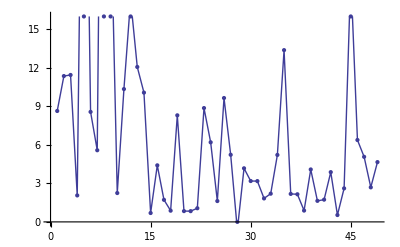

```mathematica
(*this may not be right*)
sk4=Table[k4[Flatten[cd[[;;,;;,i]]]],{i,Length[cd[[1,1]]]}]
ListPlot[sk4,Joined->True,PlotRange->{0,16},Mesh->Full]
```

{120.837,181.731,212.407,134.448,259.246,147.896,216.663,132.041,122.664,84.865,45.1334,141.641,63.6209,36.9199,28.5674,31.2847,24.8501,12.0324,10.2544,12.435,21.7361,18.1535,15.1129,31.548,13.4228,15.4385,6.8735,14.6992,12.0036,9.94556,12.427,9.2445,9.09659,7.04292,5.94071,7.90176,6.51777,4.38006,6.65223,2.94646,6.49872,2.58948,2.84843,2.17091,0.791653,0.920799,0.677373,0.402452,0.285361}

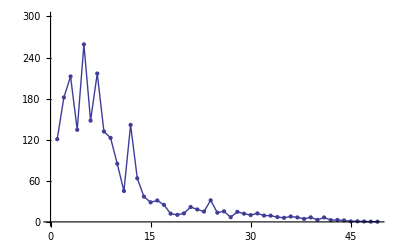

```mathematica
(* order of ICs*)
ik4=Table[k4[ic[[i]]],{i,Length[cd[[1,1]]]}]
ListPlot[ik4,Joined->True,PlotRange->{0,300},Mesh->Full]
```